# Algorithm Notes

Lars Tackman, Copenhagen 2010

Based on books :

Algorithms : A Functional Programming Approach

Currently algorithms are specified in Haskell

## Data Structures

### Lists

Sequence of similar items

#### Sorting

#### Inserting

Insertion in a ordered list
	insert x[]=[x]
	insert x (y:ys)|(x>y)=y:(insert x ys)
                                           |otherwise=x:y:ys

### Arrays

Arrays are collections of elements and they have the following properties :

A value can be accessed and updated in constant time

The update operation does not need extra space

Arrays aare preallocated in continous memory

### Trees

Tree' s consist of nodes, which may have one or more children (or descendants) and all nodes (except the root) has one predecessor (its parent). A node without a sucessor is called a leaf (or tip).Some further tree terminology is
listed below :

The depth (or hight) of a tree is its longes path from its root (the binary tree below has depth 3)

#### Binary Tree

Tree where each node has at most two sucessors. A binary tree with n nodes has the following properties :

Minimum depth = log (n + 1)

Maximum depth = n (a chain of nodes)

A full binary tree is (a tree in which every node other than the leaves has two children) is illustrated below

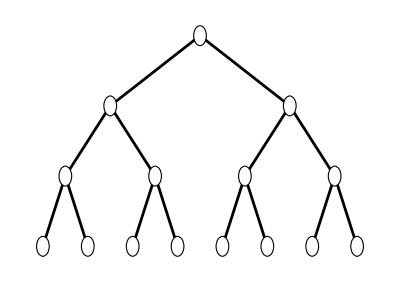

```mathematica
TreeForm[Nest[{#,#}&,x,3],VertexRenderingFunction->({EdgeForm[Black],White,Disk[#1,0.1]}&),PlotStyle->{Black,Thickness[0.005]} ]
```

Notice how each level contains the double number of nodes compared to the level above. Binary search is a divide-and-conquor algorithm, and the drawing shows how we will need (at most) 4 comparisons to find the record we are searching for in this 15 item dataset. Adding another level

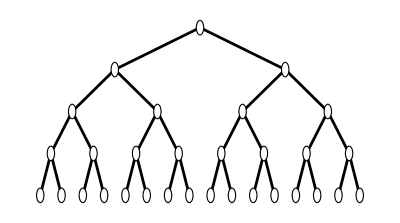

```mathematica
TreeForm[Nest[{#, #} &, x, 4], VertexRenderingFunction -> ({EdgeForm[Black], White, Disk[#1, 0.1]} &), PlotStyle -> {Black, Thickness[0.005]} ]
```

we will need 5 comparisons to find what we are search for, as the tree has only grown one level deeper when we doubled the amount of data.

1 node: log_2(1+1) = 1 comparisons.

3 nodes: log_2(3 + 1) = 2 comparisons.

7 nodes: log_2(7+1) = 3 comparisons.

As a results, the complexity of the binary search algorithm is O(log n) (logarithmic order). 

Programatically we can represent a binary tree like:

5
      | -----
  |   | 8 6
------
  | |   | 3 1 4

as
	data BinTree a = Empty | NodeBT a (BinTree a) (BinTree a) deriving Show
	 aTree = NodeBT 5 (NodeBT 8 (NodeBT 3 Empty Empty) (NodeBT 1 Empty Empty)) 
			(NodeBT 6 Empty (NodeBT 4 Empty Empty))

and converted in to a list (traversed) in the following ways :

Preorder = a node is visited before its left and right subtrees are visited.i.e : [5, 8, 3, 1, 6, 4]
	preorder Empty = []
	 preorder (NodeBT a lf rt) = [a]++ preorder lf++ preorder rt

Inorder = a node is visited after its left subtree and before its right subtrees are visited.i.e : [3, 8, 1, 5, 6, 4]
 	inorder Empty            = []
 	inorder (NodeBT a lf rt) = inorder lf ++ [a] ++ inorder rt

Postorder =  a node is visited after its left and right subtrees are visited. i.e: [3, 1, 8, 4, 6, 5]
	postorder Empty            = []
 	 postorder (NodeBT a lf rt) = postorder lf ++ postorder rt ++ [a]

## Concrete Mathematics

### Logarithms

The logarithm of a number to a given base is the power to which the base must be raised in order to produce the number. For example, the logarithm of 1000 to base 10 is 3, because 3 is the power to which ten must be raised to produce: 10^3 = 1000, so log_10(1000) = 3.

The logarithm of x to the base b is written log_b (x) or, if the base is implicit, as log(x). The bases used most often are 10 for the common logarithm, e for the natural logarithm, and 2 for the binary logarithm.

A major property of logarithms is that they map multiplication to addition, as a result of the identity

```mathematica
b^x * b^y ==b^(x+y)
```

which by taking logarithms become

```mathematica
Subscript[log, b](b^x * b^y) ==Subscript[log, b](b^(x+y))== x + y ==Subscript[log, b](b^x)+Subscript[log, b](b^y)
```

and so we have

```mathematica
log(x*y) = log(x) + log(y)
```

That is, the logarithm of the product of two numbers is the sum of the logarithms of those numbers.